```mathematica
opencldirectory="/home/chris/Programming/GPU/opencl3/";
```

## Helper

```mathematica
NotebookEvaluate[opencldirectory<>"DetectPeriodTools2.wl"]
NotebookEvaluate[opencldirectory<>"build.wl"]
```

```mathematica
GPUStructureSearch[{20, {2, 1}, 2}]
```

{151,187,189,221,635,889,15903}

#### Utility

```mathematica
Clear[ProgressMap]
ProgressMap[f_, l_List]:=Module[{stdout=PrintTemporary[""], len=Length[l], begin=TimeObject[], cur, avg,eta, tmp, cont=True, out, i=0},
out=ConstantArray[0, len];
While[cont,
i++;
out[[i]]=f[l[[i]]];
NotebookDelete[stdout];
cur=TimeObject[];avg=(cur-begin)/i;eta=begin+len*avg;stdout=PrintTemporary["Step "<>ToString[i]<>"/"<>ToString[len]<>" ("<>ToString[N[100*i/len]]<>"% complete, Avg Time "<>ToString[QuantityMagnitude[avg,"Seconds"]]<>" seconds per elem, ETA "<>DateString[eta, "DateTimeShort"]<>") ", Button["Stop", cont=False]]; 
If[i>=len, cont=False];
];
out[[;;i]]
]
ProgressMap[f_, l_Integer]:=ProgressMap[f, ConstantArray[0, l]]
```

#### Rule Generation

```mathematica
Clear[GoodRuleCondition, GoodTotalisticRuleCondition, RandomGoodRules, RandomGoodTotalisticRules];

GoodRuleCondition[ K_, R_][rule_]:=If[Length[Last[CellularAutomaton[{rule, K, R},{RandomInteger[K-1,100],0},100]]]>150,False,With[{l=Join[Table[Length[StripZeros[CellularAutomaton[{rule,K, R},{RandomInteger[K-1,100],0},{{{100}}}]]],10], Table[Length[StripZeros[CellularAutomaton[{rule, K, R},{RandomInteger[K-1,20],0},{{{100}}}]]],10]]},Mean[l]<100&&Min[l]==0&&Max[l]>0]];

GoodTotalisticRuleCondition[ K_, R_][rule_]:=If[Length[Last[CellularAutomaton[{rule, {K, 1}, R},{RandomInteger[K-1,100],0},100]]]>150,False,With[{l=Join[Table[Length[StripZeros[CellularAutomaton[{rule, {K, 1}, R},{RandomInteger[K-1,100],0},{{{100}}}]]],10], Table[Length[StripZeros[CellularAutomaton[{rule, {K, 1}, R},{RandomInteger[K-1,20],0},{{{100}}}]]],20]]},Mean[l]<100&&Min[l]==0&&Max[l]>0]];

RandomGoodRules[n_, K_:2, R_:1]:={#, K, R}&/@ParallelSelect[Union@ParallelTable[rca[{K,R},"Quiescent"->True,"Type"->"Symmetric"]["RuleNumber"], n], GoodRuleCondition[K, R]]

RandomGoodTotalisticRules[n_, K_:2, R_:1]:={#, {K, 1}, R}&/@ParallelSelect[Union@ParallelTable[rca[{K,R},"Quiescent"->True,"Type"->"Totalistic"]["TotalisticCode"], n], GoodTotalisticRuleCondition[K, R]]
```

#### Checking and Cleanup

```mathematica
Clear[DedupRuleAndRes]
DedupRuleAndRes[{rule_, res_}]:={rule, SortBy[DedupSame[Join@@ParallelMap[init|->DetectPeriod[rule, init], res]], "Canonical"]}
```

```mathematica
Clear[NonTrivialMetric];
NonTrivialMetric[{rule_, res_}]:=Which[
Length[res]==1&&res[[1, "Canonical"]]<16, False, 
AnyTrue[res, KeyExistsQ[#, "IsGliderGun"]&&#["IsGliderGun"]&], True,
Length[res]>40, False,
True, True
]

Clear[NonTrivialMetricRaw];
NonTrivialMetricRaw[{rule_, res_}]:=Which[
Length[res]==1&&res[[1]]<16, False, 
Length[res]>20, False,
True, True
]
```

#### Visualization

```mathematica
FixInteresting[]:=(interestingRules=Union[interestingRules]; interestingResults=(Last@*Sort)/@Values[GroupBy[interestingResults, First]])
ResetInteresting[]:=(interestingRules={};interestingResults={};)

ResetInteresting[]
```

```mathematica
Clear[DecentRunLength]
DecentRunLength[res_, default_]:=Round@Min[If[KeyExistsQ[res, "Period"], 2.2* res["Period"]+30, default], 500]

Clear[DecentRunLengthRaw];
DecentRunLengthRaw[rule_, res_, default_]:=Round@Min[With[{k=AnalyzeRule[rule]["Colors"]},{p=Length[FindRepeatDeterministicByStripZeros[CellularAutomaton[rule, {IntegerDigits[res, k], 0}, default]]]}, If[p!=0, 2.2*p+30, default]], 500]
```

```mathematica
Clear[DisplayRuleResult, DisplayRuleResultRaw]

DisplayRuleResult[rule_, results_, resultSteps_:200, maxNum_:50]:=With[
{k=AnalyzeRule[rule]["Colors"]},Pane[{
Button["Add", AppendTo[interestingRules, rule]; AppendTo[interestingResults, {rule, results}]],
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]],ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init["Canonical"], k], 0}, DecentRunLength[init, resultSteps]]], ClickToCopy[init["Canonical"], init]]
, {init, results[[;;UpTo[maxNum]]]}], Spacer[1]]
}, 100000]]

DisplayRuleResultRaw[rule_, results_, resultSteps_:200, maxNum_:50]:=With[
{k=AnalyzeRule[rule]["Colors"]},Pane[{
Button["Add", AppendTo[interestingRules, rule]; AppendTo[interestingResults, {rule, results}]],
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]],ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, DecentRunLengthRaw[rule, init, resultSteps]]], ClickToCopy[init]]
, {init, results[[;;UpTo[maxNum]]]}], Spacer[1]]
}, 100000]]
```

```mathematica
Clear[DisplayRuleResults]

(* resultdisplayoffset=1;
DisplayRuleResults[ress_, raw_:True, numToShow_:50,resultSteps_:200, maxNum_:50]:=(resultdisplayoffset=1;FixInteresting[];Dynamic[Column[Join[
ParallelTable[
If[raw, DisplayRuleResultRaw, DisplayRuleResult][ress[[i, 1]], ress[[i, 2]], resultSteps, maxNum], {i, resultdisplayoffset, Min[resultdisplayoffset+numToShow-1, Length[ress]]}
], 
If[
resultdisplayoffset+numToShow<Length[ress], {{
"Too many results to show, so they have been truncated.", Button["See More",resultdisplayoffset+=numToShow]
}}, {{"You've seen all results. ", Button["Close", resultdisplayoffset=Length[ress]+1; NotebookDelete[EvaluationCell[]]]}}]]], None, TrackedSymbols:>{resultdisplayoffset}]) *)

DisplayRuleResults[ress_, raw_:True, numToShow_:50,resultSteps_:200, maxNum_:50]:=(FixInteresting[];Column[
ParallelTable[If[raw, DisplayRuleResultRaw, DisplayRuleResult][i[[1]], i[[2]], resultSteps, maxNum], {i, ress}]])
```

```mathematica
VisualizeInterestingResults[steps_:100]:=Column@ParallelTable[DisplayRuleResult@@i, {i, interestingResults}]
```

```mathematica
Clear[VisualizeSingleResult];
VisualizeSingleResult[rule_List, init_List, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=ArrayPlot[RunCA[rule, init, steps], {ops}]

VisualizeSingleResult[rule_List, init_Integer, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=VisualizeSingleResult[rule, IntegerDigits[init, AnalyzeRule[rule]["Colors"]], steps, {ops}]

VisualizeSingleResult[init_Association, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=VisualizeSingleResult[init["Rule"], init["Original"], steps, {ops}]
```

#### Running

```mathematica
Clear[FullStructureSearchRaw, FullStructureSearch];
FullStructureSearchRaw[rules_, min_:0, max_:1000000, timeout_:1000]:=Module[
{ress,nontrivial},
FixInteresting[];

(* Prep memoization in a parallel manner *)
ParallelMap[AnalyzeRule, rules];

ress=ProgressMap[rule|->{rule, GPUStructureSearch[rule, min, max, timeout]}, rules];
ress=Select[ress, ListQ@*Last];
Print[Length[ress]," rules searched with results: ",Iconize[ress]];

nontrivial=ParallelSelect[ress, NonTrivialMetricRaw];
If[Length[nontrivial]<10, nontrivial=ress];
Print[Length[nontrivial], " nontrivial results: ", Iconize[nontrivial]];

DisplayRuleResults[nontrivial]
]

FullStructureSearch[rules_, min_:0, max_:1000000, timeout_:1000]:=Module[
{ress, ressDeduped, nontrivial},
FixInteresting[];

(* Prep memoization in a parallel manner *)
ParallelMap[AnalyzeRule, rules];

ress=ProgressMap[rule|->{rule, GPUStructureSearch[rule, min, max, timeout]}, rules];
ress=Select[ress, ListQ@*Last];
Print[Length[ress]," rules searched with results: ",Iconize[ress]];

(* ressDeduped=ParallelSelect[ress, Length[Last[#]]<50&]; *);
ressDeduped=Function[{rule, res}, If[Length[res]<100, {rule, res}, {rule,Union[Sort[ Join[res[[;;50]], RandomChoice[res, 50]]]]}]]@@@ress;

ressDeduped=Map[DedupRuleAndRes, ressDeduped];
Print[Total[Length/@ress], " total results deduped to ",Total[Length/@ressDeduped], " ", Iconize[ressDeduped]];

nontrivial=ParallelSelect[ressDeduped, NonTrivialMetric];
If[Length[nontrivial]<10, nontrivial=ressDeduped];
Print[Length[nontrivial], " nontrivial results: ", Iconize[nontrivial]];

 nontrivial=ressDeduped;

DisplayRuleResults[nontrivial, False]
]

FullStructureSearchQuiet[rules_, min_:0, max_:1000000, timeout_:1000]:=Module[
{ress, ressDeduped, nontrivial},
FixInteresting[];

(* Prep memoization in a parallel manner *)
ParallelMap[AnalyzeRule, rules];

ress=ProgressMap[rule|->{rule, GPUStructureSearch[rule, min, max, timeout]}, rules];
ress=Select[ress, ListQ@*Last];

ressDeduped=Map[DedupRuleAndRes, ress];

ressDeduped
]
```

## Run Example

#### Generate Decent Rules

```mathematica
ResetInteresting[]
rules=RandomGoodTotalisticRules[100, 2, 3];
Print[Length[rules]," ",Iconize[rules]];
```

11

#### Perform Initial Search, Select Interesting Rules

11 rules searched with results:

11 nontrivial results:

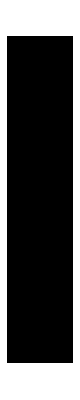
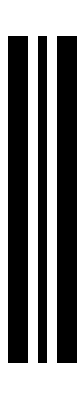
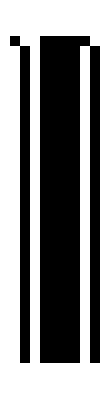
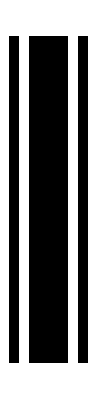
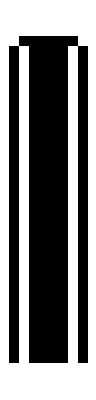
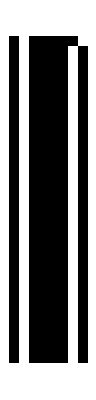
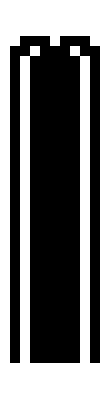
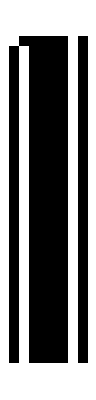
{Add,-Graphics-,-Graphics--Graphics-}
{Add,-Graphics-,-Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Add,-Graphics-,-Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics-}
{Add,-Graphics-,-Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
FullStructureSearchRaw[rules, 0, 100000]
```

#### Perform Thorough Search

2 rules searched with results:

4 total results deduped to 4

2 nontrivial results:

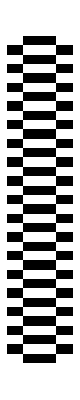
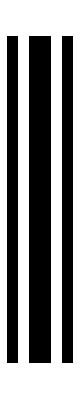
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics-}

```mathematica
FullStructureSearch[interestingRules, 0, 1000000000]
```

```mathematica
1
```

1

#### Select Interesting Initial Conditions

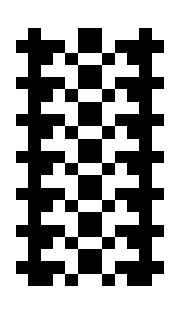

```mathematica
VisualizeSingleResult[<|"Rule"->{3389952852,2,2},"Canonical"->561,"Original"->561,"IsGliderGun"->False,"MaxDepth"->0,"MaxSteps"->200,"Period"->3,"Shift"->0,"LowestDepth"->20|>, 20, ImageSize->Small]
```

## Long Run 1 (tot k=3 r=1)

#### Generate Decent Rules

```mathematica
rules=RandomGoodTotalisticRules[10000, 3, 1];
Print[Length[rules]," ",Iconize[rules]];
```

102

#### Perform Initial Search, Select Interesting Rules

10 rules searched with results:

10 nontrivial results:

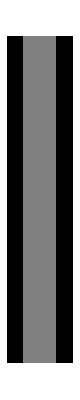
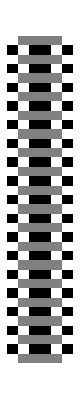
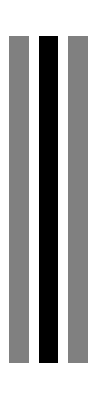
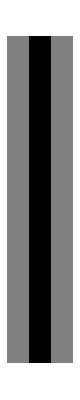
{Add,-Graphics-,-Graphics-}
{Add,-Graphics-,-Graphics-}
{Add,-Graphics-,-Graphics--Graphics-}
{Add,-Graphics-,-Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics-}
{Add,-Graphics-,-Graphics-}
{Add,-Graphics-,-Graphics-}
{Add,-Graphics-,-Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
FullStructureSearchRaw[rules, 0, 100000]
```

#### Perform Thorough Search

```mathematica
FullStructureSearch[interestingRules, 0, 1000000000]
```

3 rules searched with results:

6 total results deduped to 6

3 nontrivial results:

{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

#### Select Interesting Initial Conditions

```mathematica
Row[VisualizeSingleResult[#, 50, ImageSize->Small]&/@{<|"Rule"->{1278,{3,1},1},"Canonical"->767650,"Original"->767650,"IsGliderGun"->False,"MaxDepth"->0,"MaxSteps"->200,"Period"->25,"Shift"->0,"LowestDepth"->20|>, <|"Rule"->{141,{3,1},1},"Canonical"->172054003,"Original"->172054003,"IsGliderGun"->False,"MaxDepth"->0,"MaxSteps"->200,"Period"->16,"Shift"->0,"LowestDepth"->20|>}]
```

-Graphics--Graphics-

## Long Run 2 (k=3 r=1)

#### Generate Decent Rules

```mathematica
rules=RandomGoodRules[100000, 3, 1];
Print[Length[rules]," ",Iconize[rules]];
```

2124

#### Perform Initial Search, Select Interesting Rules

```mathematica
FullStructureSearchRaw[rules, 0, 1000000]
```

#### Perform Thorough Search

```mathematica
FullStructureSearch[interestingRules, 0, 1000000000]
```

5 rules searched with results:

10 total results deduped to 8

4 nontrivial results:

#### Select Interesting Initial Conditions

```mathematica
Row[VisualizeSingleResult[#, 50, ImageSize->Small]&/@{<|"Rule"->{306,{3,1},1},"Canonical"->215249,"Original"->215249,"IsGliderGun"->False,"MaxDepth"->0,"MaxSteps"->200,"Period"->18,"Shift"->0,"LowestDepth"->20|>, <|"Rule"->{306,{3,1},1},"Canonical"->279239,"Original"->279239,"IsGliderGun"->False,"MaxDepth"->0,"MaxSteps"->200,"Period"->7,"Shift"->-1,"LowestDepth"->20|>}]
```

-Graphics--Graphics-

## Long Run 3 (k=2 r=3)

#### Generate Decent Rules

```mathematica
rules=RandomGoodRules[10000, 2, 3];
Print[Length[rules]," ",Iconize[rules]];
```

265

#### Perform Initial Search, Select Interesting Rules

```mathematica
FullStructureSearchRaw[rules, 0, 10000000]
```

265 rules searched with results:

145 nontrivial results:

#### Perform Thorough Search

```mathematica
interestingRules
```

{{2849252904,2,2},{3389952852,2,2},{156184889221124113987013519613437236,2,3},{759092192828723256399744505693421588,2,3},{22442731057750915708427184142856164400,2,3},{25812101032193682321702956463840334528,2,3},{32761069501630941628350610796883085992,2,3},{33073656060336598790754200673428192416,2,3},{37844351503043110656442227692420146736,2,3},{44747934584103184213106546260953238580,2,3},{47917043635418287260717928399481545844,2,3},{48160796682634112441983828648750880480,2,3},{56360300644999844346728315235704048244,2,3},{58858664815922443193972486701170061448,2,3},{92865745053742518737041724757234061960,2,3},{96065303811436985004401132937190328740,2,3},{133859238966509339186028256812377059620,2,3},{137658279114538837328324044971296656496,2,3},{147397179485259907390617106820495376820,2,3},{194457127039778274087913650811125122208,2,3},{199879475214802189939922216573610955444,2,3},{204196906021884516241295387044844004912,2,3},{218860713090954712210592477853245460632,2,3},{225017250095220692249458252728060731736,2,3},{264103382170952212491550110710482280468,2,3},{266405229680463018258029170730616364704,2,3},{297806294002091822854736769235140431536,2,3},{316215309035702311525981947734680380020,2,3},{316660896454840622683309184756215647856,2,3},{319919390746253383488406484422740958816,2,3}}

```mathematica
FullStructureSearch[interestingRules, 0, 1000000000]
```

30 rules searched with results:

60 total results deduped to 60

30 nontrivial results:

3 rules searched with results:

6 total results deduped to 6

3 nontrivial results:

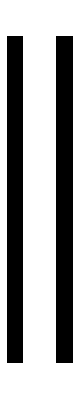
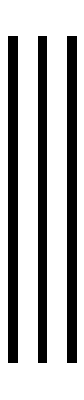
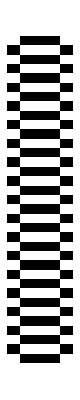
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Add,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
interestingRules={{48160796682634112441983828648750880480,2,3}, {266405229680463018258029170730616364704,2,3}, {96065303811436985004401132937190328740,2,3}};
FullStructureSearch[interestingRules, 0, 10000000000]
```

#### Select Interesting Initial Conditions

```mathematica
VisualizeSingleResult[<|"Rule"->{266405229680463018258029170730616364704,2,3},"Canonical"->2473967,"Original"->2473967,"IsGliderGun"->False,"MaxDepth"->0,"MaxSteps"->200,"Period"->30,"Shift"->0,"LowestDepth"->20|>, 200, ImageSize->Small]
```

-Graphics-

## Long Run 3.2 (k=2 r=3)

#### Generate Decent Rules

```mathematica
rules=RandomGoodRules[30000, 2, 3];
Print[Length[rules]," ",Iconize[rules]];
```

848

#### Perform Initial Search, Select Interesting Rules

```mathematica
FullStructureSearchRaw[rules, 0, 10000000]
```

848 rules searched with results:

394 nontrivial results:

#### Perform Thorough Search

```mathematica
interestingRules
```

{{48160796682634112441983828648750880480,2,3},{96065303811436985004401132937190328740,2,3},{266405229680463018258029170730616364704,2,3},{120741669778846879194572919133194880,2,3},{6788310507987364480891428353592061344,2,3},{9134762958622008190653500307723146400,2,3},{17196171003180048612909016034794283940,2,3},{19401113633038290531167787021145220136,2,3},{22152662511361273952080996238163392340,2,3},{25049482904807986002966843767694238836,2,3},{31477099345768987286605000843969855528,2,3},{44240235097650039148336055649431034704,2,3},{49111081453209127972014176979509452580,2,3},{52774972202236171683778639054890310232,2,3},{57753697197709767557033744910758107432,2,3},{66996878105545338731143890271348808628,2,3},{70709357375601996334867213575174202164,2,3},{77441222225934918451549903882036644148,2,3},{90532959886347362535805886793046702120,2,3},{95977195196732954919014033969361071208,2,3},{101133655025701660369800255412678902932,2,3},{104931026295350111769172412194228350772,2,3},{104944988982047737064386691577541376144,2,3},{110498860031952801361762698523497775520,2,3},{144791249858099592004043278434684661408,2,3},{160725050306177788693196724098254202132,2,3},{164345047178974922344987870534524048080,2,3},{169460768479764862973440935358998564872,2,3},{172640996014791719331611603717513798292,2,3},{173013774802054257345328187483667238544,2,3},{176031408999646470007782415653314896704,2,3},{209175693309599792994005980685342596528,2,3},{210884415567900237252388948876682555416,2,3},{211813514647456436989268745527975187152,2,3},{221136811191540533095090909833786689248,2,3},{226199955817820573705916691409698112852,2,3},{240436475290582751494640207091570583844,2,3},{247759269884142320779378626009433573940,2,3},{250199946682782865431787330835937627940,2,3},{258775536244938769734884454615941383232,2,3},{271414363550268450611330515959636040036,2,3},{282737016792599617241161928586800548480,2,3},{287678469601282591390180274541204957208,2,3},{287671693460130085021623765665144900320,2,3},{299487394228216260896006481833710814416,2,3},{308738398381456042735328428750519038820,2,3},{330482846952385865664327774775587389984,2,3},{199879475214802189939922216573610955444,2,3},{225017250095220692249458252728060731736,2,3}}

```mathematica
FullStructureSearch[interestingRules, 0, 1000000000]
```

49 rules searched with results:

98 total results deduped to 98

49 nontrivial results:

#### Select Interesting Initial Conditions

```mathematica
Row[VisualizeSingleResult[#,200, ImageSize->Small]&/@{
<|"Rule"->{144791249858099592004043278434684661408,2,3},"Canonical"->2656357271314320340303,"Original"->495822922,"IsGliderGun"->False,"MaxDepth"->0,"MaxSteps"->200,"Period"->98,"Shift"->0,"LowestDepth"->20|>,
<|"Rule"->{271414363550268450611330515959636040036,2,3},"Canonical"->83562883711001,"Original"->83562883711001,"IsGliderGun"->False,"MaxDepth"->0,"MaxSteps"->200,"Period"->31,"Shift"->0,"LowestDepth"->20|>,
<|"Rule"->{17196171003180048612909016034794283940,2,3},"Canonical"->150079,"Original"->150079,"IsGliderGun"->False,"MaxDepth"->0,"MaxSteps"->200,"Period"->60,"Shift"->-24,"LowestDepth"->20|>

}]
```

-Graphics--Graphics--Graphics-

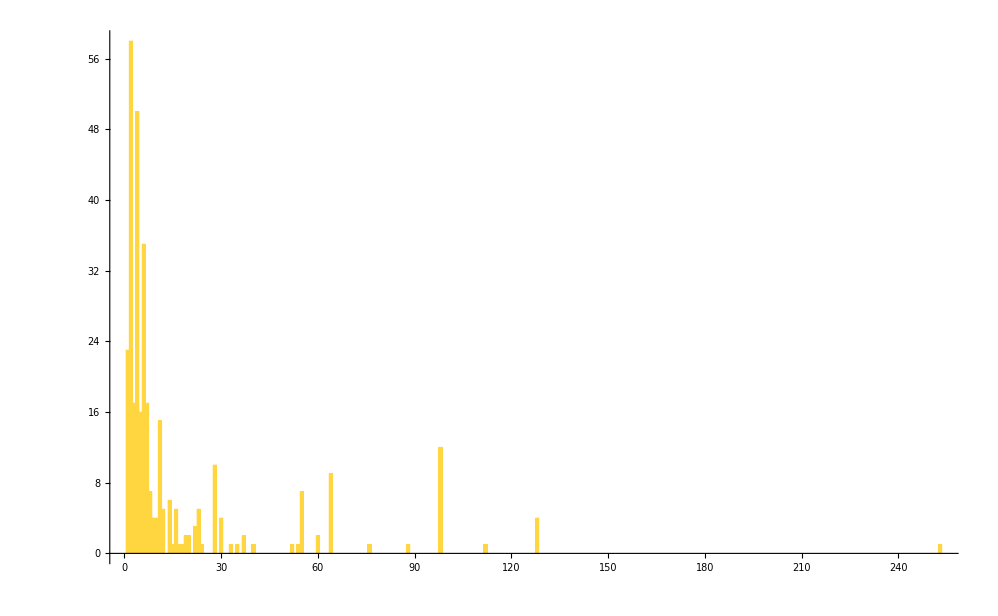

```mathematica
Histogram[Flatten[interestingResults[[All, 2]]][[All, "Period"]], {1}, PlotRange->All]
```

```mathematica
AArrayPlot[{271414363550268450611330515959636040036,2,3}, 1281593, 200]
```

-Graphics-

```mathematica
GPUStructureSearch[{271414363550268450611330515959636040036,2,3}, 0, 100000000]
```

{83562883711001}

```mathematica
AArrayPlot[{271414363550268450611330515959636040036,2,3}, RandomInteger[100000000000]]
```

-Graphics-

## Long Run 4 (k=4 r=1)

#### Generate Decent Rules

```mathematica
rules=RandomGoodRules[10000, 4, 1];
Print[Length[rules]," ",Iconize[rules]];
```

455

```mathematica
rules=;
```

#### Perform Initial Search, Select Interesting Rules

```mathematica
FullStructureSearchRaw[rules, 0, 10000000]
```

454 rules searched with results:

186 nontrivial results:

#### Perform Thorough Search

```mathematica
interestingRules
```

{{4663207722134789154619953883335585564,4,1},{10708107981403203024349989470618222908,4,1},{27390025456893930444044196853987293708,4,1},{38162126798349566268738375399613971840,4,1},{48025167572242222058111390830663302288,4,1},{53048472903065062737884704395288693056,4,1},{76091649241615787610125855137559994892,4,1},{167789705057737679490826776687586427968,4,1},{177478631080244680856259575580716172360,4,1},{250971588582534420390817482048668338192,4,1},{284636095346840571388263005053335085376,4,1},{326674556512408700786857756260456261192,4,1}}

```mathematica
FullStructureSearch[interestingRules, 0, 1000000000, 1000]
```

12 rules searched with results:

24 total results deduped to 24

12 nontrivial results:

```mathematica
FullStructureSearch[interestingRules, 0, 10000000000, 1000]
```

11 rules searched with results:

22 total results deduped to 22

11 nontrivial results:

#### Select Interesting Initial Conditions

```mathematica
Row[VisualizeSingleResult[#,200, ImageSize->Small]&/@{


}]
```

```mathematica
AArrayPlot[{61456402163624945211017545221180604172,4,1}, RandomInteger[4^50], 500]
```

-Graphics-

```mathematica
Clear[BinarySearchFirstOccasion];
BinarySearchFirstOccasion[rule_, init_, max_:1000000]:=Module[{l=0, r=Min[max, init+10], mid, detected, res},
TimeConstrained[
While[r>l,
Pause[0.5];
mid=Floor[(l + r)/2];
If[r==l+1,mid=RandomChoice[{r, l}]];

res=Quiet[Check[GPUStructureSearch[rule, 0, mid, 30], 0]];
If[res===0, Print["ERROR"],
detected=MemberQ[res, init];
PrintTemporary["l: ", l, ", r: ", r, ", mid: ", mid, ", detected: ", detected];
If[detected, r=mid, l=mid];
];
Pause[0.5];
];

,30];

r
]

BinarySearchFirstOccasion[{20, {2, 1}, 2}, 15903]

ArrayPlot[CellularAutomaton[{20, {2, 1}, 2}, {IntegerDigits[%, 2], 0}, 50]]
```

196

-Graphics-

-Graphics-

```mathematica
GPUStructureSearch[{20, {2, 1}, 2}, 0, 10000000]
```

{151,187,189,221,635,889,15903,125231,595703,610999,624623}

-Graphics-

## Auto Rare Glider Gun Finder

```mathematica
lateGliderGunCondition[rule_]:=TimeConstrained[!AnyTrue[SortBy[DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&,Union@RandomChoice[GPUStructureSearch[rule, 0, 10000], 100]]], #Canonical&], #IsGliderGun&]&&AnyTrue[SortBy[DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&,Union@RandomChoice[GPUStructureSearch[rule, 0, 1000000], 20]]], #Canonical&], #IsGliderGun&], 30, True]
lateGliderGunConditionStrict[rule_]:=TimeConstrained[!AnyTrue[SortBy[DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&,Union@RandomChoice[GPUStructureSearch[rule, 0, 10000], 100]]], #Canonical&], #IsGliderGun&]&&AnyTrue[SortBy[DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&,Union@RandomChoice[GPUStructureSearch[rule, 0, 1000000], 20]]], #Canonical&], #IsGliderGun&], 30, False]
```

```mathematica
lateGliderGunCondition[{1329, {3,  1}, 1}]

lateGliderGunCondition[{20, {2,  1}, 2}] (* no glider gun *)

lateGliderGunCondition[{52, {2,  1}, 2}] (* not late *)
```

True

False

False

```mathematica
randrules=Range[0, 2186];
randrules=ParallelSelect[randrules, IntegerDigits[#, 3, 1]=={0}&];
randrules={#, {3, 1}, 1}&/@ParallelSelect[randrules, Or@@Table[GoodTotalisticRuleCondition[3, 1][#], 100]&];
Length[randrules]
Iconize[randrules]
```

140

```mathematica
ProgressMap[If[lateGliderGunCondition[#], #, Nothing]&, randrules]
```

{{63,{3,1},1},{438,{3,1},1},{681,{3,1},1},{870,{3,1},1},{1329,{3,1},1},{1521,{3,1},1}}

```mathematica
ProgressMap[rule|->GPUStructureSearch[rule, 0, 100000, 100], ]
```

```mathematica
allrules={{63,{3,1},1},{438,{3,1},1},{681,{3,1},1},{870,{3,1},1},{1329,{3,1},1},{1521,{3,1},1}};
allresults=;
```

```mathematica
Length/@allresults[[All, 2]]
```

{1032,1253,39,23,87,291}

#### 3

```mathematica
rule=allrules[[3]]
res=GPUStructureSearch[rule, 0, 10000];
Length[res]
```

{681,{3,1},1}

23

```mathematica
2228
```

```mathematica
ClickToCopy[AArrayPlot[rule, #], #]&/@res
```

{-Graphics-2042,-Graphics-2228,-Graphics-3092,-Graphics-6653,-Graphics-6714592520,-Graphics-9268383472,-Graphics-20143851926,-Graphics-27855709594,-Graphics-59547190577,-Graphics-83567260681,-Graphics-178643341103,-Graphics-247575858181,-Graphics-554432062838,-Graphics-742718420494,-Graphics-1663235840390,-Graphics-2186227046482,-Graphics-4707201811109,-Graphics-6558684327925,-Graphics-45377012194772,-Graphics-60439920807580,-Graphics-60439924920760,-Graphics-136131036585242,-Graphics-177742321626022}

```mathematica
AArrayPlot[{681,{3,1},1}, 64157, 2000]
```

-Graphics-

```mathematica
AArrayPlot[{681,{3,1},1}, 68000, 1200]
```

-Graphics-

```mathematica
CellularAutomaton[{681,{3,1},1}, {IntegerDigits[6653, 3], 0}, {{{15}}}]
```

{2,2,0,0,0,0,0,0,0,0,2,2,2,1}

```mathematica
CellularAutomaton[{681,{3,1},1}, {IntegerDigits[6653, 3], 0}, {{{20}}}]
```

{2,2,0,0,0,0,0,0,0,0,1,2,2,0,2,1,2}

```mathematica
Reverse[{2,2,0,0,0,0,0,0,0,0,1,2,2,0,2,1,2}]
```

{2,1,2,0,2,2,1,0,0,0,0,0,0,0,0,2,2}

```mathematica
Row[{AArrayPlot[{681,{3,1},1},{2,1,2,0,2,2,1,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,2,2,2,1}, 200, ImageSize->Medium], AArrayPlot[{681,{3,1},1},{2,2,0,0,0,0,0,0,0, 0,0,2,2,2,1}, 2000, ImageSize->Medium], 
AArrayPlot[{681,{3,1},1},{2,2,0,0,0,0,0,0,0,0,2,2,2,1}, 400, ImageSize->Medium]AArrayPlot[{681,{3,1},1},{2,2,0,0,0,0,0,0,0, 0,0, 0,0, 2,2,2,1}, 500, ImageSize->Medium]}]
```

-Graphics--Graphics--Graphics- -Graphics-

#### 4

```mathematica
rule=allrules[[4]]
res=DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&, GPUStructureSearch[rule, 0, 100000]]][[All, "Canonical"]];
Length[res]
```

{870,{3,1},1}

14

```mathematica
ClickToCopy[AArrayPlot[rule, #], #]&/@res
```

{-Graphics-24650,-Graphics-91718,-Graphics-68,-Graphics-40,-Graphics-121,-Graphics-364,-Graphics-1093,-Graphics-598144,-Graphics-1620688,-Graphics-1794433,-Graphics-4862065,-Graphics-5383300,-Graphics-16149901,-Graphics-1308062236}

```mathematica
AArrayPlot[rule, 24650, 200]
```

-Graphics-

#### 5

```mathematica
rule=allrules[[5]]
res=DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&, GPUStructureSearch[rule, 0, 100000]]][[All, "Canonical"]];
Length[res]
```

{1329,{3,1},1}

18

```mathematica
ClickToCopy[AArrayPlot[rule, #], #]&/@res
```

{-Graphics-38411,-Graphics-38480,-Graphics-60416,-Graphics-97171,-Graphics-97439,-Graphics-400,-Graphics-1199,-Graphics-32476,-Graphics-97114,-Graphics-97357,-Graphics-97427,-Graphics-292070,-Graphics-22960,-Graphics-184315,-Graphics-22234,-Graphics-20990041,-Graphics-525304562024518979,-Graphics-9571}

```mathematica
AArrayPlot[rule, 38411, 2000]
```

-Graphics-

#### 6

```mathematica
rule=allrules[[6]]
res= Sort@GPUStructureSearch[rule, 0, 10000];
Length[res]
```

{1521,{3,1},1}

60

```mathematica
ClickToCopy[AArrayPlot[rule, #, 200], #]&/@res[[;;10]]
```

{-Graphics-2,-Graphics-4,-Graphics-1001,-Graphics-2513,-Graphics-3010,-Graphics-4001,-Graphics-5036,-Graphics-7562,-Graphics-8051,-Graphics-9004}

```mathematica
rule=allrules[[2]]
res= Sort@GPUStructureSearch[rule, 0, 10000];
Length[res]
```

{438,{3,1},1}

142

```mathematica
ClickToCopy[AArrayPlot[rule, #, 500], #]&/@res
```

{-Graphics-34,-Graphics-106,-Graphics-122,-Graphics-266,-Graphics-289,-Graphics-305,-Graphics-311,-Graphics-359,-Graphics-410,-Graphics-443,-Graphics-2221,-Graphics-2222,-Graphics-2228,-Graphics-2239,-Graphics-2320,-Graphics-2341,-Graphics-6647,-Graphics-6667,-Graphics-7034,-Graphics-7133,-Graphics-7139,-Graphics-7141,-Graphics-7142,-Graphics-7147,-Graphics-7153,-Graphics-7163,-Graphics-8009,-Graphics-8026,-Graphics-8042,-Graphics-8044,-Graphics-8053,-Graphics-9488,-Graphics-8633218,-Graphics-257311528,-Graphics-37145412535,-Graphics-83682826718,-Graphics-370177886392,-Graphics-1382684734112,-Graphics-2118803040355,-Graphics-2254639026088,-Graphics-4309865890126,-Graphics-6593294944033,-Graphics-13936097899930,-Graphics-20011554864487,-Graphics-20315797425703,-Graphics-36734805959164,-Graphics-42647098250605,-Graphics-45608989161262,-Graphics-87806438511308,-Graphics-902425166834965,-Graphics-3022122294696751,-Graphics-13927674995549215,-Graphics-58542471398338124,-Graphics-81133772212928746,-Graphics-91819716108029546,-Graphics-127420853172233830,-Graphics-277195210162724020,-Graphics-297623047770968894,-Graphics-744570992008795723,-Graphics-826435918139999309,-Graphics-881625844418820449,-Graphics-1801102529632361258,-Graphics-6531433411125135619,-Graphics-8,-Graphics-344852000,-Graphics-32420441225184931448,-Graphics-1914394638793189513484672,-Graphics-10849,-Graphics-1183,-Graphics-5658253510,-Graphics-4124865948296,-Graphics-298879}

## Discovery Rate Analysis

```mathematica
GPUStructureSearch[{20, {2, 1}, 2}, 0, 100000]
```

{151,187,189,221,635,889,15903}

14

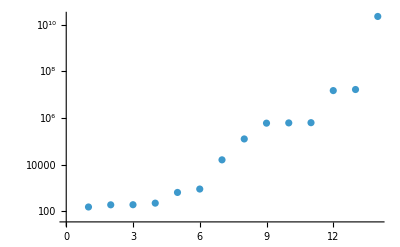

```mathematica
ListLogPlot[EchoFunction[Length]@GPUStructureSearch[{20,{2,1},2}, 0, 1000000000]]
```

```mathematica
res=GPUStructureSearch[{20,{2,1},2}, 0, 10000000];
Length[res]
```

53

```mathematica
res=GPUStructureSearch[{438,{3,1},1}, 0, 1000000];
Length[res]
```

7082

```mathematica
res=GPUStructureSearch[{1329,{3,1},1}, 0, 100000];
Length[res]
```

1103

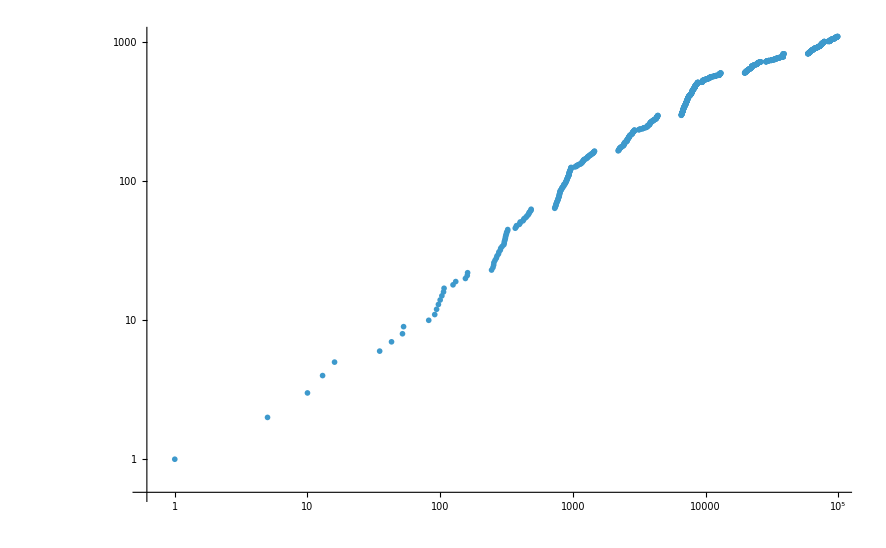

```mathematica
ListLogLogPlot[Transpose[{res, Range[Length[res]]}]]
```

```mathematica
DetectPeriodMemo[args__]:=DetectPeriodMemo[args]=DetectPeriod[args]
```

```mathematica
rule={438,{3,1},1};
inits=GPUStructureSearch[rule, 0, 10000];
ress=DedupSame[SortBy[Join@@ParallelMap[DetectPeriodMemo[rule, #]&, inits], #Original&]];
resss=Sort@ress[[All, "Original"]]

ressss=Transpose[{resss, Range[Length[resss]]}];
```

{5,34,35,106,106,106,106,106,122,266,289,289,305,311,359,410,443,1069,1076,1096,1103,1112,2221,2222,3139,3166,6647,6667,7034,7133,8009,8026,8044,8053,8060,8060,8063,8063,9302}

```mathematica
rule={1329, {3, 1}, 1};
inits=GPUStructureSearch[rule, 0, 1000000];
ress=DedupSame[SortBy[Join@@ParallelMap[DetectPeriodMemo[rule, #]&, inits], #Original&]];
resss=Sort@ress[[All, "Original"]]

ressss=Transpose[{resss, Range[Length[resss]]}];
```

{1,52,400,457,800,916,1199,2617,32476,38411,38480,60416,97114,97171,97172,97357,97427,97439,115226,115396,185075,223531,291341,291443,292000,346003,346028,541375,546964,554254,632917,654856,659197,873557,874471}

```mathematica
rule={20, {2, 1}, 2};
inits=GPUStructureSearch[rule, 0, 1000000000];
ress=DedupSame[SortBy[Join@@ParallelMap[DetectPeriodMemo[rule, #]&, inits], #Original&]];
resss=Sort@ress[[All, "Original"]]

ressss=Transpose[{resss, Range[Length[resss]]}];
```

{151,187,189,195,635,125231,595703,610999,14871103,256296063}

```mathematica
ListLogLinearPlot[ParallelMap[Style[Callout[#, Tooltip[ClickToCopy[AArrayPlot[rule, #[[1]],60], #[[1]]],AArrayPlot[rule, #[[1]], 300]], LabelVisibility->All],If[AnyTrue[DetectPeriodMemo[rule, #[[1]]], #IsGliderGun&], Red, Blue]]&,ressss], LabelingSize->{Automatic, 25}, Joined->True, Filling->Axis]
```

-Graphics-

```mathematica
GPUStructureSearchMemo[args__]:=GPUStructureSearch[args]=GPUStructureSearch[args]
```

```mathematica
ProgressMap[Function[{rule},TimeConstrained[
inits=GPUStructureSearchMemo[rule, 0, 1000000000];
inits=inits[[;;UpTo[10000]]];
ress=DedupSame[SortBy[Join@@ParallelMap[DetectPeriodMemo[rule, #]&, inits], #Original&]];
resss=Sort@ress[[All, "Original"]];

ressss=Transpose[{resss, Range[Length[resss]]}];

ListLogLinearPlot[ParallelMap[Style[Callout[#, Tooltip[ClickToCopy[AArrayPlot[rule, #[[1]],60], #[[1]]],AArrayPlot[rule, #[[1]], 300]], LabelVisibility->All],If[AnyTrue[DetectPeriodMemo[rule, #[[1]]], #IsGliderGun&], Red, Blue]]&,ressss], LabelingSize->{Automatic, 25}, Joined->True, Filling->Axis,InterpolationOrder->0, PlotRange->{{1, 1000000000}, All}], 30]], 

{{20, {2, 1}, 2}}]
```

{-Graphics-}

```mathematica
ProgressMap[Function[{rule},TimeConstrained[
inits=GPUStructureSearchMemo[rule, 0, 1000000];
inits=inits[[;;UpTo[10000]]];
ress=DedupSame[SortBy[Join@@ParallelMap[DetectPeriodMemo[rule, #]&, inits], #Original&]];
resss=Sort@ress[[All, "Original"]];

ressss=Transpose[{resss, Range[Length[resss]]}];
AppendTo[ressss, {1000000, 0}];

ListLogLinearPlot[ParallelMap[Style[Callout[#, Tooltip[ClickToCopy[AArrayPlot[rule, #[[1]],60], #[[1]]],AArrayPlot[rule, #[[1]], 300]], LabelVisibility->All],If[AnyTrue[DetectPeriodMemo[rule, #[[1]]], #IsGliderGun&], Red, Blue]]&,ressss], LabelingSize->{Automatic, 25}, Joined->True, Filling->Axis,InterpolationOrder->0, PlotRange->{{1, 1000000}, All}], 30]], 

{{2849252904,2,2},{3389952852,2,2},{156184889221124113987013519613437236,2,3},{759092192828723256399744505693421588,2,3},{22442731057750915708427184142856164400,2,3},{25812101032193682321702956463840334528,2,3},{32761069501630941628350610796883085992,2,3},{33073656060336598790754200673428192416,2,3},{37844351503043110656442227692420146736,2,3},{44747934584103184213106546260953238580,2,3},{47917043635418287260717928399481545844,2,3},{48160796682634112441983828648750880480,2,3},{56360300644999844346728315235704048244,2,3},{58858664815922443193972486701170061448,2,3},{92865745053742518737041724757234061960,2,3},{96065303811436985004401132937190328740,2,3},{133859238966509339186028256812377059620,2,3},{137658279114538837328324044971296656496,2,3},{147397179485259907390617106820495376820,2,3},{194457127039778274087913650811125122208,2,3},{199879475214802189939922216573610955444,2,3},{204196906021884516241295387044844004912,2,3},{218860713090954712210592477853245460632,2,3},{225017250095220692249458252728060731736,2,3},{264103382170952212491550110710482280468,2,3},{266405229680463018258029170730616364704,2,3},{297806294002091822854736769235140431536,2,3},{316215309035702311525981947734680380020,2,3},{316660896454840622683309184756215647856,2,3},{319919390746253383488406484422740958816,2,3}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

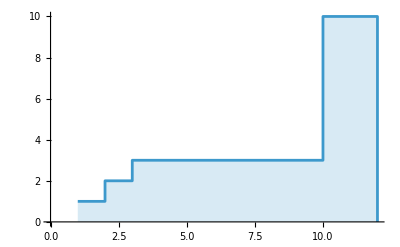

```mathematica
ListPlot[{{1, 1} , {2, 2}, {3, 3}, {10, 10}, {12, 0}}, Joined->True, InterpolationOrder->0, Filling->Axis, PlotRange->{{0, 12}, All}]
```

```mathematica
Column[%]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

## more

```mathematica
k=2;R=2;
randrules=Range[0, 2^(2R+2)-1];
Length[randrules]
randrules=ParallelSelect[randrules, IntegerDigits[#, k, 1]=={0}&];
Length[randrules]
randrules={#, {k, 1},R}&/@ParallelSelect[randrules, Or@@Table[GoodTotalisticRuleCondition[k, R][#], 100]&];
Length[randrules]
Iconize[randrules]
```

64

32

6

```mathematica
ProgressMap[If[lateGliderGunCondition[#], #, Nothing]&, randrules]
```

{}

```mathematica
k=2;R=3;
randrules=Range[0, 2^(2R+2)-1];
Length[randrules]
randrules=ParallelSelect[randrules, IntegerDigits[#, k, 1]=={0}&];
Length[randrules]
randrules={#, {k, 1},R}&/@ParallelSelect[randrules, Or@@Table[GoodTotalisticRuleCondition[k, R][#], 100]&];
Length[randrules]
Iconize[randrules]
```

256

128

23

```mathematica
ProgressMap[If[lateGliderGunCondition[#], #, Nothing]&, randrules]
```

{{232,{2,1},3}}

```mathematica
rule={232,{2,1},3}
res= Sort@GPUStructureSearch[rule, 0, 300000];
Length[res]
```

{232,{2,1},3}

30

```mathematica
ClickToCopy[AArrayPlot[rule, #, 100], #]&/@res[[;;20]]
```

{-Graphics-39,-Graphics-57,-Graphics-107,-Graphics-189,-Graphics-381,-Graphics-765,-Graphics-1533,-Graphics-3069,-Graphics-6141,-Graphics-24359,-Graphics-29309,-Graphics-48935,-Graphics-58621,-Graphics-98087,-Graphics-117245,-Graphics-181963,-Graphics-183947,-Graphics-196391,-Graphics-214477,-Graphics-216461}

```mathematica
181963
```

```mathematica
k=4;R=1;
randrules=Range[0,k^(2R+2)-1];
Length[randrules]
randrules=ParallelSelect[randrules, IntegerDigits[#, k, 1]=={0}&];
Length[randrules]
randrules={#, {k, 1},R}&/@ParallelSelect[randrules, Or@@Table[GoodTotalisticRuleCondition[k, R][#], 100]&];
Length[randrules]
Iconize[randrules]
```

256

64

3

```mathematica
ProgressMap[If[lateGliderGunConditionStrict[#], #, Nothing]&, randrules]
```

{}

```mathematica
k=2;R=4;
randrules=Range[0,(k^(2R+2))-1];
Length[randrules]
randrules=ParallelSelect[randrules, IntegerDigits[#, k, 1]=={0}&];
Length[randrules]
randrules={#, {k, 1},R}&/@ParallelSelect[randrules, Or@@Table[GoodTotalisticRuleCondition[k, R][#], 100]&];
Length[randrules]
Iconize[randrules]
```

1024

512

79

```mathematica
ProgressMap[If[lateGliderGunConditionStrict[#], #, Nothing]&, randrules]
```

```mathematica
k=2;R=1;
randrules=Range[0,k^((k-1)(2R+1)+1)-1];
Length[randrules]
randrules=ParallelSelect[randrules, IntegerDigits[#, k, 1]=={0}&];
Length[randrules]
randrules={#, {k, 1},R}&/@ParallelSelect[randrules, Or@@Table[GoodTotalisticRuleCondition[k, R][#], 100]&];
Length[randrules]
Iconize[randrules]
ProgressMap[If[lateGliderGunConditionStrict[#], #, Nothing]&, randrules]
```

16

8

2

{}

```mathematica
k=2;R=4;
randrules=Range[0,k^((k-1)(2R+1)+1)-1];
Length[randrules]
randrules=ParallelSelect[randrules, IntegerDigits[#, k, 1]=={0}&];
Length[randrules]
randrules={#, {k, 1},R}&/@ParallelSelect[randrules, Or@@Table[GoodTotalisticRuleCondition[k, R][#], 100]&];
Length[randrules]
Iconize[randrules]
ProgressMap[If[lateGliderGunConditionStrict[#], #, Nothing]&, randrules]
```

1024

512

79

RandomChoice::lrwl: The items for choice {} should be a nonempty list or a rule weights -> choices.

RandomChoice::lrwl: The items for choice 100 should be a nonempty list or a rule weights -> choices.

RandomChoice::lrwl: The items for choice {} should be a nonempty list or a rule weights -> choices.

CellularAutomaton::initn: The initial condition specification {{},0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

CompiledCodeFunction::argtype: Argument type at position 1 does not match function signature.

FromDigits::nlst: The expression CellularAutomaton[{548,{2,1},4},{{},0},200] is not a list of digits or a string of valid digits.

CellularAutomaton::initn: The initial condition specification {{},0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

FromDigits::nlst: The expression CellularAutomaton[200,{{},0},{548,{2,1},4}] is not a list of digits or a string of valid digits.

FromDigits::nlst: The expression 1 is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

RandomChoice::lrwl: The items for choice {} should be a nonempty list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

CellularAutomaton::initn: The initial condition specification {{},0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

FromDigits::nlst: The expression CellularAutomaton[200,{{},0},{548,{2,1},4}] is not a list of digits or a string of valid digits.

CellularAutomaton::initn: The initial condition specification {{},0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

FromDigits::nlst: The expression CellularAutomaton[{548,{2,1},4},{{},0},200] is not a list of digits or a string of valid digits.

FromDigits::nlst: The expression 1 is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

Join::incpt: Incompatible elements in Join[RandomChoice[{}],<|Rule→{548,{2,1},4},Canonical→Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{548,{2,1},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{548,{2,1},4},{{},0},200],2]]],Original→0,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→{Log[2200/FromDigits[1,2]]/Log[2],Log[2198/FromDigits[1,2]]/Log[2]},LowestDepth→20|>] cannot be joined.

Union::smtst: Application of the SameTest function yielded (#1[Canonical]==#2[Canonical]&)[RandomChoice[{}],<|Rule→{548,{2,1},4},Canonical→Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{548,{2,1},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{548,{2,1},4},{{},0},200],2]]],Original→0,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→{Log[2200/FromDigits[1,2]]/Log[2],Log[2198/FromDigits[1,2]]/Log[2]},LowestDepth→20|>], which evaluates to RandomChoice[{}][Canonical]==Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{548,{«2»},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{548,{«2»},4},{{},0},200],2]]]. The SameTest function must evaluate to True or False at every pair of elements.

Join::incpt: Incompatible elements in Join[<|Rule→{548,{2,1},4},Canonical→Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{548,{2,1},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{548,{2,1},4},{{},0},200],2]]],Original→0,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→{Log[2200/FromDigits[1,2]]/Log[2],Log[2198/FromDigits[1,2]]/Log[2]},LowestDepth→20|>,RandomChoice[{}]] cannot be joined.

General::stop: Further output of Join::incpt will be suppressed during this calculation.

Do::iterb: Iterator {soln,Join[<|Rule→{548,{2,1},4},Canonical→Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{548,{2,1},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{548,{2,1},4},{{},0},200],2]]],Original→0,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→{Log[2200/FromDigits[1,2]]/Log[2],Log[2198/FromDigits[1,2]]/Log[2]},LowestDepth→20|>,RandomChoice[{}]]} does not have appropriate bounds.

RandomChoice::lrwl: The items for choice {} should be a nonempty list or a rule weights -> choices.

CellularAutomaton::initn: The initial condition specification {{},0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

CompiledCodeFunction::argtype: Argument type at position 1 does not match function signature.

FromDigits::nlst: The expression CellularAutomaton[{548,{2,1},4},{{},0},200] is not a list of digits or a string of valid digits.

CellularAutomaton::initn: The initial condition specification {{},0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

FromDigits::nlst: The expression CellularAutomaton[200,{{},0},{548,{2,1},4}] is not a list of digits or a string of valid digits.

FromDigits::nlst: The expression 1 is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

CellularAutomaton::initn: The initial condition specification {{},0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

General::stop: Further output of CellularAutomaton::initn will be suppressed during this calculation.

Union::smtst: Application of the SameTest function yielded (#1[Canonical]==#2[Canonical]&)[RandomChoice[{}],<|Rule→{548,{2,1},4},Canonical→Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{548,{2,1},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{548,{2,1},4},{{},0},200],2]]],Original→0,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→{Log[2200/FromDigits[1,2]]/Log[2],Log[2198/FromDigits[1,2]]/Log[2]},LowestDepth→20|>], which evaluates to RandomChoice[{}][Canonical]==Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{548,{«2»},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{548,{«2»},4},{{},0},200],2]]]. The SameTest function must evaluate to True or False at every pair of elements.

Do::iterb: Iterator {soln,Join[<|Rule→{548,{2,1},4},Canonical→Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{548,{2,1},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{548,{2,1},4},{{},0},200],2]]],Original→0,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→{Log[2200/FromDigits[1,2]]/Log[2],Log[2198/FromDigits[1,2]]/Log[2]},LowestDepth→20|>,RandomChoice[{}]]} does not have appropriate bounds.

RandomChoice::lrwl: The items for choice {} should be a nonempty list or a rule weights -> choices.

CellularAutomaton::initn: The initial condition specification {{},0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

CompiledCodeFunction::argtype: Argument type at position 1 does not match function signature.

FromDigits::nlst: The expression CellularAutomaton[{656,{2,1},4},{{},0},200] is not a list of digits or a string of valid digits.

CellularAutomaton::initn: The initial condition specification {{},0} should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

FromDigits::nlst: The expression CellularAutomaton[200,{{},0},{656,{2,1},4}] is not a list of digits or a string of valid digits.

FromDigits::nlst: The expression 1 is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

Union::smtst: Application of the SameTest function yielded (#1[Canonical]==#2[Canonical]&)[RandomChoice[{}],<|Rule→{656,{2,1},4},Canonical→Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{656,{2,1},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{656,{2,1},4},{{},0},200],2]]],Original→0,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→{Log[2632/FromDigits[1,2]]/Log[2],Log[2630/FromDigits[1,2]]/Log[2]},LowestDepth→20|>], which evaluates to RandomChoice[{}][Canonical]==Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{656,{«2»},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{656,{«2»},4},{{},0},200],2]]]. The SameTest function must evaluate to True or False at every pair of elements.

General::stop: Further output of Union::smtst will be suppressed during this calculation.

Do::iterb: Iterator {soln,Join[<|Rule→{656,{2,1},4},Canonical→Min[FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[200,{{},0},{656,{2,1},4}],2]],FindRepeatDeterministicByStripZeros[FromDigits[CellularAutomaton[{656,{2,1},4},{{},0},200],2]]],Original→0,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→{Log[2632/FromDigits[1,2]]/Log[2],Log[2630/FromDigits[1,2]]/Log[2]},LowestDepth→20|>,RandomChoice[{}]]} does not have appropriate bounds.

General::stop: Further output of Do::iterb will be suppressed during this calculation.

{}

```mathematica
k=3;R=1;
randrules=Range[0,k^((k-1)(2R+1)+1)-1];
Length[randrules]
randrules=ParallelSelect[randrules, IntegerDigits[#, k, 1]=={0}&];
Length[randrules]
randrules={#, {k, 1},R}&/@ParallelSelect[randrules, Or@@Table[GoodTotalisticRuleCondition[k, R][#], 100]&];
Length[randrules]
Iconize[randrules]
randrules=randrules[[;;UpTo[200]]];
ProgressMap[If[lateGliderGunConditionStrict[#], #, Nothing]&, randrules]
```

2187

729

143

{{1329,{3,1},1},{1842,{3,1},1}}

```mathematica
k=3;R=2;
randrules=Range[0,k^((k-1)(2R+1)+1)-1];
Length[randrules]
randrules=ParallelSelect[randrules, IntegerDigits[#, k, 1]=={0}&];
Length[randrules]
randrules={#, {k, 1},R}&/@ParallelSelect[randrules, Or@@Table[GoodTotalisticRuleCondition[k, R][#], 100]&];
Length[randrules]
Iconize[randrules]
randrules=randrules[[;;UpTo[200]]];
ProgressMap[If[lateGliderGunConditionStrict[#], #, Nothing]&, randrules]
```

```mathematica
AArrayPlot[{1842,{3,1},1}, RandomInteger[3^100]]
```

-Graphics-

```mathematica
GPUStructureSearch[{1842, {3, 1}, 1}, 0, 100000]
```

{1,5,10,23,28,34,40,41,50,68,89,95,104,122,149,158,203,244,250,262,266,293,311,320,374,412,428,455,608,611,629,734,772,779,788,806,820,833,874,878,880,887,896,910,932,937,1070,1103,1220,1258,1312,1319,1400,1418,1456,1823,1832,2198,2252,2360,2386,2390,2426,2440,2446,2447,2462,2470,2492,2494,2498,2554,2608,2609,2624,2633,2635,2644,2656,2662,2669,2684,2732,2741,2800,2813,2858,2860,2876,2878,2885,2887,3265,3308,3314,3317,3362,3371,3389,3422,3424,3656,3710,3875,3877,3904,3950,3956,3974,4082,4091,4127,4199,4253,4370,4372,5450,5468,5477,5489,5495,5504,5642,5660,6562,6568,6580,6613,6616,6679,6724,6730,6746,6791,6902,6940,6950,7054,7066,7099,7124,7160,7162,7169,7286,7322,7340,7364,7366,7381,7387,7421,7445,7447,7450,7484,7493,7700,7721,7808,7826,7868,7907,7922,7925,7934,7970,7988,8002,8008,8026,8038,8071,8192,8204,8206,8222,8366,8402,8411,8420,8435,8465,8474,8492,8555,8573,8578,8621,8627,8659,8690,8692,8708,8710,8719,9547,9638,9682,9691,9701,9710,9772,9922,9923,10013,10025,10085,10111,10148,10166,10256,10259,10708,10942,10987,11104,11120,11165,11276,11324,11444,11471,11543,11554,11572,11606,11624,11660,11696,11714,11738,11858,11867,12011,12094,12101,12110,12128,12146,12272,12335,12344,12353,12382,12515,12524,12607,12614,12632,12740,12769,12830,12839,12857,12875,12902,13118,16304,16349,16352,16358,16385,16403,16415,16430,16439,16484,16568,16820,16928,19688,19696,19733,19742,19772,19778,19805,19850,19858,19895,19952,19976,20044,20057,20059,20129,20138,20156,20165,20174,20182,20219,20258,20264,20294,20312,20411,20432,20434,20474,20492,20537,20543,20620,20704,20705,20708,20732,20822,20891,20893,20918,20920,21020,21137,21146,21154,21191,21200,21230,21236,21263,21317,21380,21410,21434,21470,21491,21508,21625,21653,21668,21722,21731,21799,21805,21911,21931,21962,22016,22100,22145,22192,22211,22240,22244,22315,22397,22433,22448,22807,22930,22942,22990,23105,23107,23110,23156,23165,23369,23389,23420,23474,23704,23717,23758,23798,23906,23960,24008,24040,24046,24062,24070,24107,24116,24146,24152,24179,24224,24232,24269,24326,24350,24431,24433,24503,24512,24530,24539,24611,24616,24622,24667,24703,24773,24806,24808,24848,24866,24911,24917,24994,25052,25123,25202,25241,25259,25298,25306,25322,25325,25403,25421,25430,25484,25664,25673,25736,25738,25742,25780,25781,25811,25826,25835,25882,25904,25912,25973,25979,25981,25985,26051,26069,26102,26105,26123,26176,26186,26204,26213,28438,28600,28772,28798,28924,29140,29158,29240,29399,29768,29831,29848,29849,29950,30011,30092,30128,30280,30361,30371,30436,30443,30497,30560,30562,30578,30580,30589,30659,30668,30698,30722,30767,30776,30823,30832,30995,31211,31462,32351,32810,32855,32864,32927,32972,33017,33098,33179,33251,33260,33278,33287,33296,33341,33416,33434,33665,33827,33830,33854,33944,34142,34259,34331,34333,34334,34423,34556,34628,34637,34682,34691,34709,34745,34801,34855,34883,34895,34934,34952,34961,34979,34988,35033,35222,35384,35386,35393,35422,35519,35555,35837,36086,36227,36323,36329,36392,36410,36428,36584,36791,36896,36932,36959,37004,37052,37058,37130,37168,37220,37295,37715,37724,37850,37868,37886,37913,37967,38075,38096,38219,38246,38284,38354,38390,38414,38510,38516,38579,38597,38615,38687,38705,38912,46268,47987,48866,48884,48893,48905,48911,48920,48947,48950,48965,48974,49028,49046,49049,49055,49058,49073,49082,49112,49148,49154,49163,49190,49208,49229,49247,49289,49514,49532,49625,50354,50462,59060,59090,59099,59114,59126,59171,59180,59222,59234,59279,59293,59299,59311,59317,59327,59347,59371,59413,59414,59419,59441,59450,59455,59461,59489,59519,59546,59576,59585,59612,59747,59819,59846,59860,59866,59878,59882,59914,59920,59963,59990,60008,60134,60152,60164,60182,60305,60341,60346,60352,60364,60368,60406,60487,60499,60518,60548,60557,60572,60584,60629,60638,60679,60685,60730,60737,60746,60757,60769,60775,60785,60805,60829,60880,60911,61016,61073,61097,61154,61169,61205,61286,61313,61334,61358,61370,61396,61448,61540,61610,61660,61669,61675,61684,61693,61705,61711,61772,61820,61844,61939,61961,62006,62017,62042,62096,62150,62177,62204,62233,62269,62285,62302,62303,62315,62317,62323,62335,62336,62462,62546,62744,62771,62792,62816,62828,62854,62875,62897,62933,62971,62983,62989,62998,63082,63118,63127,63133,63163,63223,63296,63325,63397,63434,63464,63473,63488,63500,63545,63554,63596,63608,63653,63673,63685,63691,63701,63721,63745,63787,63788,63793,63815,63824,63835,63863,63893,63932,63973,63979,64013,64040,64058,64067,64193,64220,64240,64252,64256,64288,64294,64337,64364,64382,64406,64460,64475,64531,64549,64576,64678,64711,64727,64855,65134,65140,65188,65332,65399,65401,65413,65456,65563,65569,65620,65732,65822,65894,65974,65975,65986,66002,66008,66010,66011,66058,66067,66085,66257,66389,66412,66430,66524,66605,66650,66686,66794,66812,66821,66875,66947,67055,67064,67190,67237,67283,67352,67432,67433,67442,67456,67483,67489,67537,67721,68870,69166,69350,69379,69470,70106,70268,70348,70349,70360,70376,70382,70384,70385,70432,70441,70459,70523,70544,70546,70844,71006,71062,71080,71131,71134,71152,71158,71182,71251,71252,71344,71395,71401,71440,71510,71536,71548,71549,71566,71618,71623,71668,71719,71731,71737,71755,71780,71786,71860,71863,71881,71887,71911,71953,72007,72008,72020,72074,72088,72089,72122,72212,72221,72248,72293,72302,72356,72401,72421,72433,72439,72449,72493,72536,72541,72563,72572,72583,72611,72641,72698,72707,72734,72869,72941,72968,72988,73000,73004,73042,73085,73112,73130,73274,73286,73304,73427,73463,73474,73486,73490,73528,73609,73621,73810,73825,73832,73850,73856,73906,73918,74053,74068,74158,74242,74285,74300,74318,74356,74408,74435,74456,74480,74492,74518,74570,74662,74732,74797,74806,74815,74833,74894,74942,74966,75083,75323,75325,75337,75424,75425,75437,75445,75457,75458,75506,75593,75595,75662,75700,75758,75776,75781,75877,76081,76085,76106,76154,76160,76262,76267,76316,76322,76324,76391,76490,76517,76649,76784,76838,76856,76910,76919,76937,76946,76973,77000,77018,77023,77090,77185,77204,77215,77240,77324,77342,77378,77423,77432,77477,77504,77509,77539,77671,77726,77738,77740,77753,77755,77800,77849,77876,77888,77914,77921,77933,77944,77969,78125,78134,78230,78242,78368,78392,78449,78473,78485,78506,78512,78577,78593,78631,78665,78701,78719,85669,86380,86398,87236,87353,87614,88178,88190,88196,88199,88262,88468,88630,88748,88796,88999,89072,89242,89312,89420,89492,89546,89714,89720,89899,89977,90014,90151,90194,90230,90275,90392,90502,90635,90661,90664,90682,90787,90908,90988,91058,91150,91168,91309,91310,91394,91472,91492,91661,91679,91712,91733,91796,91814,92039,92084,92120,92159,92174,92203,92204,92222,92318,92417,92525,92543,92570,92644,92707,92896,94370,94418,94435,95147,95182,95560,95660,96551,96659,97172,97216,97909,98152,98456,98465,98492,98537,98546,98600,98645,98665,98683,98693,98737,98780,98807,98816,98827,98855,98885,98942,98951,98978,99113,99185,99212,99232,99248,99286,99329,99356,99374,99518,99530,99548,99671,99707,99718,99734,99772,99853,99914,99923,99950,99995}

```mathematica
SortBy[DedupSame[Join@@ParallelMap[DetectPeriod[{1842,{3,1},1}, #]&, ]], #Original&]
```

```mathematica
Row[ClickToCopy[AArrayPlot[{1842,{3,1},1}, #, 200, ImageSize->Medium], #]&/@[[All,"Canonical" ]], Spacer[1]]
```

-Graphics-10-Graphics-23-Graphics-40-Graphics-122-Graphics-68-Graphics-455-Graphics-203-Graphics-29848-Graphics-36086-Graphics-608-Graphics-236756968-Graphics-1103-Graphics-65620-Graphics-3317-Graphics-78918991-Graphics-108257-Graphics-9922-Graphics-1823-Graphics-1832-Graphics-3314-Graphics-7253509-Graphics-9923-Graphics-265831-Graphics-5477-Graphics-5468-Graphics-267941-Graphics-29849-Graphics-29768-Graphics-2395133-Graphics-11444-Graphics-16484-Graphics-16439-Graphics-268646-Graphics-89546-Graphics-24616-Graphics-35386-Graphics-49532-Graphics-48950-Graphics-49289-Graphics-196952-Graphics-2394427-Graphics-2417762-Graphics-803759-Graphics-267917-Graphics-267944-Graphics-1328603-Graphics-65108164-Graphics-803803-Graphics-89312-Graphics-803756

```mathematica
FindRepeatDeterministicByStripZeros[RunCA[{1842,{3,1},1}, 24616, 5000]]//Length
```

1760

```mathematica
AArrayPlot[{1842,{3,1},1}, 48950, 1000]
```

-Graphics-

```mathematica
k=3;R=2;
randrules=Range[0,k^((k-1)(2R+1)+1)-1];
Length[randrules]
randrules=ParallelSelect[randrules, IntegerDigits[#, k, 1]=={0}&];
Length[randrules]
randrules={#, {k, 1},R}&/@ParallelSelect[randrules, Or@@Table[GoodTotalisticRuleCondition[k, R][#], 1]&];
Length[randrules]
```

177147

59049

5648

```mathematica
Iconize[randrules]
randrules=randrules[[;;UpTo[200]]];
```

```mathematica
ProgressMap[If[lateGliderGunConditionStrict[#], #, Nothing]&, randrules]
```